```mathematica
Clear["Global`*"]
```

```mathematica
(* Quadratic function, constant damping 

η = γ t

*)
```

```mathematica
DSolve[{q'[t]==Exp[-γ t] p[t],p'[t]==-Exp[γ t]q[t],q[0]==a,p[0]==0},{q[t],p[t]},t]//FullSimplify
```

{{p[t]→-(2 a ⅇ^((t γ)/2) Sinh[1/2 t √(-4+γ^2)])/(√(-4+γ^2)),q[t]→a ⅇ^(-(t γ)/2) (Cosh[1/2 t √(-4+γ^2)]+(γ Sinh[1/2 t √(-4+γ^2)])/(√(-4+γ^2)))}}

```mathematica
P[t_,γ_,x_]:=-(2  x  ⅇ^((t γ)/2) Sin[1/2 t √(4-γ^2)])/(√(4-γ^2))
Q[t_,γ_,x_]:=x ⅇ^(-(t γ)/2) (Cos[1/2 t √(4-γ^2)]+(γ Sin[1/2 t √(4-γ^2)])/(√(4-γ^2)))
H[q_,p_,t_,γ_]:=(1/2)Exp[-γ t] p^2 + Exp[γ t] q^2/2
```

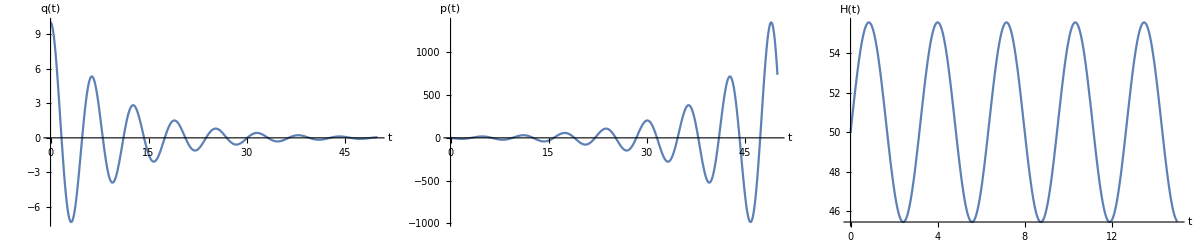

```mathematica
γ=.2;
g=GraphicsRow[{
Plot[Q[t,γ,10], {t,0,50},
PlotRange->Full,
AxesLabel->{Style[HoldForm[t],12],Style[HoldForm[q[t]],12]}],
Plot[P[t,γ,10], {t,0,50},
PlotRange->Full,
AxesLabel->{Style[HoldForm[t],12],Style[HoldForm[p[t]],12]}],
Plot[H[Q[t,γ,10],P[t,γ,10],γ,t], {t,0,15},
PlotRange->Full,
AxesLabel->{Style[HoldForm[t],12],Style[HoldForm[H[t]],12]},PlotRangePadding->{0,0}]
},Spacings->{0,0}]
(*b=Plot[P[t,γ,10],{t,0,100},PlotRange->Full,PlotLegends->Placed[{HoldForm[p[t]]},{{.5,1},{.5,.3}}],LabelStyle->{GrayLevel[0]},ImageSize->Small,TicksStyle->Small]
c=Plot[H[Q[t,γ,10],P[t,γ,10],t,γ],{t,0,100},PlotLegends->Placed[{HoldForm[H[q[t],p[t],t]]},{{.5,1},{.5,.3}}],LabelStyle->{GrayLevel[0]},ImageSize->Small,TicksStyle->Small]*)
```

```mathematica
Export["/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_const.pdf",g]
```

/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_const.pdf

```mathematica
Nesterov[q0_,γ_,T_,MaxIter_]:=(
h=T/MaxIter;
t=0;
q=q0;
p=0;
μ=Exp[-γ h];
data={};
For[k=1,k<=MaxIter,k++,

oldq=q;
q=q+h μ p;
g=q;
p=μ p-h g;
q=oldq+h p;
t=t+h;
numham=H[q,p Exp[γ t],t,γ];

trueham=H[Q[t,γ,q0],P[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];

];

Return[data];
)

Euler1[q0_,γ_,T_,MaxIter_]:=(
h=T/MaxIter;
t=0;
q=q0;
p=0;
data={};
For[k=1,k<=MaxIter,k++,

g=q;
p=p-h Exp[γ t]g;
q=q+h Exp[-γ t]p;
t=t+h;
numham=H[q,p,t,γ];

trueham=H[Q[t,γ,q0],P[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];

];

Return[data];
)

LeapFrog1[q0_,γ_,T_,MaxIter_]:=(
h=T/MaxIter;
t=0;
q=q0;
p=0;
data={};
For[k=1,k<=MaxIter,k++,

g=q;
p=p-(h/2) Exp[γ t]g;
q=q+(h/2)Exp[-γ t]p;
t=t+h;
q=q+(h/2)Exp[-γ t]p;
g=q;
p=p-(h/2) Exp[γ t]g;
numham=H[q,p,t,γ];

trueham=H[Q[t,γ,q0],P[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];
];

Return[data];
)
LeapFrog2[q0_,γ_,T_,MaxIter_]:=(
h=T/MaxIter;
t=0;
q=q0;
p=0;
data={};
For[k=1,k<=MaxIter,k++,

t=t+h/2;
q=q+(h/2)Exp[-γ t]p;
g=q;
p=p-h(Exp[γ t])g;
q=q+(h/2)Exp[-γ t]p;
t=t+h/2;
numham=H[q,p,t,γ];

trueham=H[Q[t,γ,q0],P[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];
];
Return[data];
)

Yoshida1[q0_,γ_,T_,MaxIter_]:=(
ϵ=T/MaxIter;
t=0;
q=q0;
p=0;
data={};
κ=2^(1/3)//N;
For[k=1,k<=MaxIter,k++,

a=1/(2-κ);
h=a *ϵ;
g=q;
p=p-(h/2) Exp[γ t]g;
q=q+(h/2)Exp[-γ t]p;
t=t+h;
q=q+(h/2)Exp[-γ t]p;
g=q;
p=p-(h/2) Exp[γ t]g;

b=-κ/(2-κ);
h=b *ϵ;
p=p-(h/2) Exp[γ t]g;
q=q+(h/2)Exp[-γ t]p;
t=t+h;
q=q+(h/2)Exp[-γ t]p;
g=q;
p=p-(h/2) Exp[γ t]g;

h=a * ϵ;
p=p-(h/2) Exp[γ t]g;
q=q+(h/2)Exp[-γ t]p;
t=t+h;
q=q+(h/2)Exp[-γ t]p;
g=q;
p=p-(h/2) Exp[γ t]g;

numham=H[q,p,t,γ];

trueham=H[Q[t,γ,q0],P[t,γ,q0],t,γ];
AppendTo[data,{t,Abs[trueham-numham]}];
];
Return[data];
)
```

```mathematica
dataEu=Euler1[10.,0.2,50,10000];
dataLf=LeapFrog1[10.,0.2,50,10000];
dataYo=Yoshida1[10.,0.2,50,10000];
```

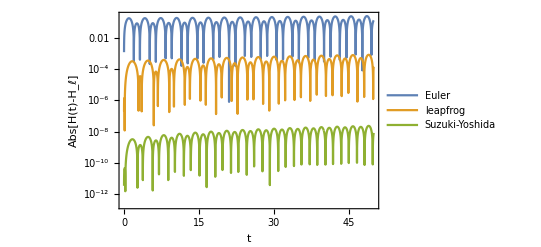

```mathematica
dataEu2 = Take[dataEu,{1,-1,1}];
dataLf2 = Take[dataLf,{1,-1,1}];
dataYo2=Take[dataYo,{1,-1,1}];
g=ListLogPlot[{dataEu2[[All,{1,2}]],dataLf2[[All,{1,2}]],dataYo2[[All,{1,2}]]},Frame->True, FrameLabel->{Style[HoldForm[t],FontSize->14], Style[HoldForm[Abs[H[t] - Subscript[H, ℓ]] ],FontSize->14]},PlotLegends->Placed[{"Euler", "leapfrog", "Suzuki-Yoshida"},Top],
Joined->True]
```

```mathematica
dataLf=LeapFrog1[10.,0.2,50,30000];
dataNe=Nesterov[10.,0.2,50,30000];
```

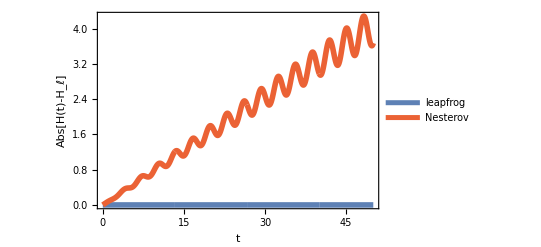

```mathematica
g=ListPlot[{dataLf[[All,{1,2}]],dataNe[[All,{1,2}]]},
PlotStyle->{{ColorData[97,"ColorList"][[1]],Thickness[0.01]},{ColorData[97,"ColorList"][[4]],Thickness[0.01]}},
Frame->True, FrameLabel->{Style[HoldForm[t],FontSize->14], Style[HoldForm[Abs[H[t] - Subscript[H, ℓ]] ],FontSize->14]},PlotLegends->Placed[{"leapfrog", "Nesterov"},Top],
Joined->True,
PlotRangePadding->{0,.5}]
```

```mathematica
Export["/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_const_nest1.pdf",g]
```

/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_const_nest1.pdf

```mathematica
dataLf=LeapFrog1[10.,-1.0,50,30000];
dataNe=Nesterov[10.,-1.0,50,30000];
```

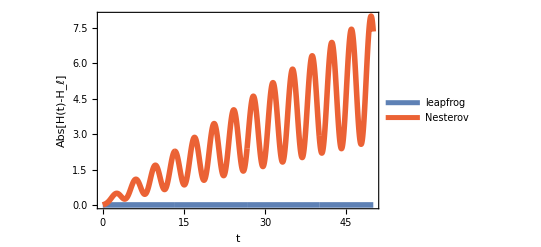

```mathematica
g=ListPlot[{dataLf[[All,{1,2}]],dataNe[[All,{1,2}]]},
PlotStyle->{{ColorData[97,"ColorList"][[1]],Thickness[0.01]},{ColorData[97,"ColorList"][[4]],Thickness[0.01]}},
Frame->True, FrameLabel->{Style[HoldForm[t],FontSize->14], Style[HoldForm[Abs[H[t] - Subscript[H, ℓ]] ],FontSize->14]},PlotLegends->Placed[{"leapfrog", "Nesterov"},Top],
Joined->True,PlotRangePadding->{0,.8}]
```

```mathematica
Export["/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_const_nest2.pdf",g]
```

/Users/gui/my_papers/dissipative_symplectic/arxiv/quad_const_nest2.pdf

```mathematica
ColorData[97,"ColorList"][[]]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}